## Chapter 2 /3 Linear ODEs of Second And Higher Order

### General Solution,Initial Value Problem:

```mathematica
ode = y''[x] + y'[x] -2y[x] == 0
```

-2 y[x]+y'[x]+y''[x]==0

```mathematica
ode2 =D[y[x],x,x] + D[y[x],x]-2y[x]== 0
```

-2 y[x]+y'[x]+y''[x]==0

```mathematica
sol =DSolve[ode,y[x],x]
```

{{y[x]→ⅇ^(-2 x) C[1]+ⅇ^x C[2]}}

```mathematica
sol2 = DSolve[ode2,y[x],x]
```

{{y[x]→ⅇ^(-2 x) C[1]+ⅇ^x C[2]}}

```mathematica
ypartic = DSolve[{ode,y[0]==4,y'[0]==-5},y[x],x]
```

{{y[x]→ⅇ^(-2 x) (3+ⅇ^(3 x))}}

```mathematica
Simplify[%]
```

{{y[x]→3 ⅇ^(-2 x)+ⅇ^x}}

```mathematica
yprime =D[sol,x]
```

{{y'[x]→-2 ⅇ^(-2 x) C[1]+ⅇ^x C[2]}}

```mathematica
y0 =sol[[1,1,2]]/.x-> 0
```

C[1]+C[2]

```mathematica
yprime0 =yprime [[1,1,2]]/.x-> 0
```

-2 C[1]+C[2]

```mathematica
s =Solve[{y0,yprime0 }== {4,5},{C[1],C[2]}]
```

{{C[1]→-1/3,C[2]→13/3}}

```mathematica
sol[[1,1,2]]/.s
```

{-1/3 ⅇ^(-2 x)+(13 ⅇ^x)/3}

```mathematica
A ={{1,1},{-2,1}}
```

{{1,1},{-2,1}}

```mathematica
b ={4,-5};
```

```mathematica
c =LinearSolve[A,b]
```

{3,1}

```mathematica
Y =ypartic[[1,1,2]]
```

ⅇ^(-2 x) (3+ⅇ^(3 x))

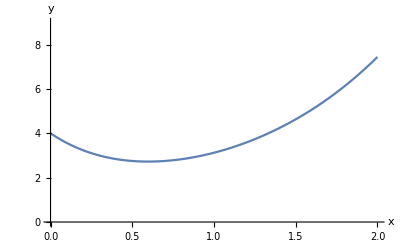

```mathematica
Plot[Y ,{x,0,2},PlotRange->{0,9},AxesLabel->{x,y}]
```

## Mass-Spring System,Complex Characteristics Roots,Damped Oscillations::

```mathematica
ode1 = y''[t]+0.2y'[t] + 4.01 y[t] == 0
```

4.01 y[t]+0.2 y'[t]+y''[t]==0

```mathematica
yp =DSolve[{ode1,y[0] ==0,y'[0] == 2},y[t],t]
```

{{y[t]→1. ⅇ^(-0.1 t) Sin[2. t]}}

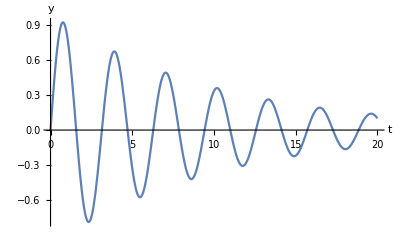

```mathematica
Plot[yp[[1,1,2]],{t,0,20},AxesLabel->{t,y}]
```

## The Three Cases Of Damping::

```mathematica
Clear[y1,y2,y3]
```

```mathematica
ode3 =y1''[t]+(1/2) y1'[t]+y1[t] ==0
```

y1[t]+y1'[t]/2+y1''[t]==0

```mathematica
y1[t]+y1'[t]/2+y1''[t]==0
```

y1[t]+y1'[t]/2+y1''[t]==0

```mathematica
ode4 =y2''[t] +2y2'[t]+y2[t] == 0
```

y2[t]+2 y2'[t]+y2''[t]==0

```mathematica
ode5 =y3''[t]+3y3'[t]+y3[t]==0
```

y3[t]+3 y3'[t]+y3''[t]==0

```mathematica
yp1 =DSolve[{ode3,y1[0]==1,y1'[0]==0},y1[t],t]
```

{{y1[t]→1/15 ⅇ^(-t/4) (15 Cos[(√15 t)/4]+√15 Sin[(√15 t)/4])}}

```mathematica
yp2 =DSolve[{ode4,y2[0]==1,y2'[0]==0},y2[t],t]
```

{{y2[t]→ⅇ^-t (1+t)}}

```mathematica
yp3 =DSolve[{ode5 ,y3[0]==1,y3'[0]==0},y3[t],t]
```

{{y3[t]→1/10 (5 ⅇ^((-3/2-(√5)/2) t)-3 √5 ⅇ^((-3/2-(√5)/2) t)+5 ⅇ^((-3/2+(√5)/2) t)+3 √5 ⅇ^((-3/2+(√5)/2) t))}}

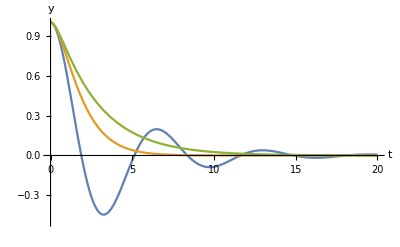

```mathematica
Plot[{yp1[[1,1,2]],yp2[[1,1,2]],yp3[[1,1,2]]},{t,0,20},PlotRange->{-0.5,1},AxesLabel->{t,y}]
```

## The Three Cases For An Euler-Cauchy Equation

```mathematica
(* Solve x^2 y'' + axy' + y =0 *)
```

```mathematica
ode6 =x^2  y1''[x] + (3/2) x  y1'[x]+y1[x]==0
```

y1[x]+3/2 x y1'[x]+x^2 y1''[x]==0

```mathematica
ode7 = x^2 y2''[x]+3x y2'[x] +y2[x]==0
```

y2[x]+3 x y2'[x]+x^2 y2''[x]==0

```mathematica
ode8 = x^2 y3''[x] +4x y3'[x] +y3[x]==0
```

y3[x]+4 x y3'[x]+x^2 y3''[x]==0

```mathematica
yp4 =DSolve[{ode6,y1[1]==1,y1'[1]==0},y1[x],x]
```

{{y1[x]→(15 Cos[1/4 √15 Log[x]]+√15 Sin[1/4 √15 Log[x]])/(15 x^(1/4))}}

```mathematica
yp5 =DSolve[{ode7,y2[1]==1,y2'[1]==0},y2[x],x]
```

{{y2[x]→(1+Log[x])/x}}

```mathematica
yp6=DSolve[{ode8,y3[1]==1,y3'[1]==0},y3[x],x]
```

{{y3[x]→1/10 x^(-3/2-(√5)/2) (5-3 √5+5 x^(√5)+3 √5 x^(√5))}}

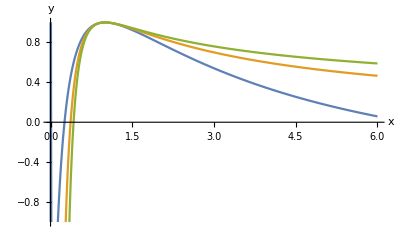

```mathematica
Plot[{yp4[[1,1,2]],yp5[[1,1,2]],yp6[[1,1,2]]},{x,0,6},PlotRange->{-1,1},AxesLabel->{x,y}]
```

## Wronskian::

```mathematica
(* y'' +p1(x)y'+p0(x)y =0 *)
```

```mathematica
y7 =Cos[k x]; y8=Sin[k x];
```

```mathematica
W =y7 D[y8,x] - y8 D[y7,x]
```

k Cos[k x]^2+k Sin[k x]^2

```mathematica
Simplify[%]
```

k

```mathematica
B = {{y7,y8},{D[y7,x],D[y8,x]}}
```

{{Cos[k x],Sin[k x]},{-k Sin[k x],k Cos[k x]}}

```mathematica
%//MatrixForm
```

(Cos[k x] | Sin[k x]
-k Sin[k x] | k Cos[k x])

```mathematica
y = Det[B]
```

k Cos[k x]^2+k Sin[k x]^2

```mathematica
Simplify[%]
```

k

```mathematica
y9=Exp[-x];y10 =Exp[x]; y11=Exp[2 x];
```

```mathematica
y12 ={y9,y10,y11}
```

{ⅇ^-x,ⅇ^x,ⅇ^(2 x)}

```mathematica
C1 ={y12,D[y12,x],D[y12,x,x]}
```

{{ⅇ^-x,ⅇ^x,ⅇ^(2 x)},{-ⅇ^-x,ⅇ^x,2 ⅇ^(2 x)},{ⅇ^-x,ⅇ^x,4 ⅇ^(2 x)}}

```mathematica
%//MatrixForm
```

(ⅇ^-x | ⅇ^x | ⅇ^(2 x)
-ⅇ^-x | ⅇ^x | 2 ⅇ^(2 x)
ⅇ^-x | ⅇ^x | 4 ⅇ^(2 x))

```mathematica
Det[C1]
```

6 ⅇ^(2 x)

## Non-Homogenous Linear ODEs::

```mathematica
(* y'' +2y'+101y =10.4e^x ,y(0)=1.1, y'(0)=-0.9 *)
```

```mathematica
Clear[y]
```

```mathematica
ode9 = y''[x]+2y'[x]+101y[x] == 10.4 Exp[x]
```

101 y[x]+2 y'[x]+y''[x]==10.4 ⅇ^x

```mathematica
yp12 = DSolve[{ode9,y[0] == 1.1 ,y'[0] == -0.9},y[x],x]
```

{{y[x]→0.1 ⅇ^(-1. x) (10. Cos[10. x]+1. ⅇ^(2. x) Cos[10. x]^2+1. ⅇ^(2. x) Sin[10. x]^2)}}

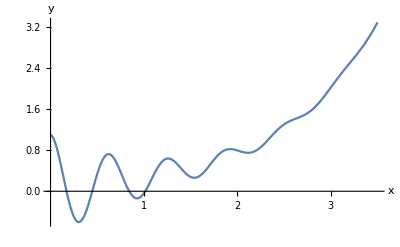

```mathematica
Plot[yp12[[1,1,2]],{x,0,3.5},Ticks->{{1,2,3},Automatic},AxesLabel->{x,y}]
```

## Solution By Undetermined Coefficients::

```mathematica
(* y'' -3y'+2y =e^x *)
```

```mathematica
Clear[y]
```

```mathematica
Ly = y''[x]-3y'[x] +2y[x]
```

2 y[x]-3 y'[x]+y''[x]

```mathematica
r =Exp[x]
```

ⅇ^x

```mathematica
yh =DSolve[Ly ==0,y[x],x]
```

{{y[x]→ⅇ^x C[1]+ⅇ^(2 x) C[2]}}

```mathematica
yp13 =C x Exp[x]
```

C ⅇ^x x

```mathematica
Ly == r
```

2 y[x]-3 y'[x]+y''[x]==ⅇ^x

```mathematica
Ly ==r /. {y[x]-> yp13, y'[x] ->D[yp13,x],y''[x]-> D[yp13,x,x]}
```

2 C ⅇ^x+3 C ⅇ^x x-3 (C ⅇ^x+C ⅇ^x x)==ⅇ^x

```mathematica
sol1 =Simplify[%]
```

(1+C) ⅇ^x==0

```mathematica
C0 =Solve[sol1,C]
```

{{C→-1}}

```mathematica
yh[[1,1,2]]
```

ⅇ^x C[1]+ⅇ^(2 x) C[2]

```mathematica
yp14 = yp13/. C -> C0 [[1,1,2]]
```

-ⅇ^x x

```mathematica
ygon =yh[[1,1,2]]+ yp14
```

-ⅇ^x x+ⅇ^x C[1]+ⅇ^(2 x) C[2]

```mathematica
DSolve[Ly == r,y[x],x]
```

{{y[x]→-ⅇ^x (1+x)+ⅇ^x C[1]+ⅇ^(2 x) C[2]}}

## Solution By Variation Of Parameters::

```mathematica
(* y''+y =Secx *)
```

```mathematica
Clear[y]
```

```mathematica
Ly1 = y''[x] + y[x]
```

y[x]+y''[x]

```mathematica
p =Sec[x]
```

Sec[x]

```mathematica
yh1 = DSolve[Ly == 0 ,y[x],x]
```

{{y[x]→C[1] Cos[x]+C[2] Sin[x]}}

```mathematica
y14  =Cos[x]; y15 =Sin[x];
```

```mathematica
W1 =y14 D[y15,x]-y15 D[y14,x]
```

Cos[x]^2+Sin[x]^2

```mathematica
Simplify[%]
```

Sin[x]

```mathematica
yp15 = - y14 Integrate[y15  p/W1 ,x]+ y15 Integrate[y14  p/W1 ,x]
```

Cos[x] Log[Cos[x]]+x Sin[x]

```mathematica
ygen =yh1[[1,1,2]]+ yp15
```

C[1] Cos[x]+Cos[x] Log[Cos[x]]+x Sin[x]+C[2] Sin[x]

```mathematica
DSolve[Ly1 == p ,y[x],x]
```

{{y[x]→C[1] Cos[x]+Cos[x] Log[Cos[x]]+x Sin[x]+C[2] Sin[x]}}

## Forced Vibration ,Resonance , Beats::

```mathematica
(* y'' +y = Cost *)
```

```mathematica
Clear[y,y1,y2]
```

```mathematica
ode14 = y''[t]+y[t] == Cos[t]
```

y[t]+y''[t]==Cos[t]

```mathematica
sol3  = DSolve[ode14,y[t],t]
```

{{y[t]→C[1] Cos[t]+C[2] Sin[t]+1/4 (2 Cos[t]^3+2 t Sin[t]+Sin[t] Sin[2 t])}}

```mathematica
sol4  = Simplify[%]
```

{{y[t]→1/2 (Cos[t]+2 C[1] Cos[t]+t Sin[t]+2 C[2] Sin[t])}}

```mathematica
y16 =sol4[[1,1,2,2,3]]
```

t Sin[t]

```mathematica
Plot[y1,{t,0,50},AxesLabel-> {t,y16}]
```

-Graphics-

```mathematica
ode5 =y2''[t] +y2[t]==0.19 Cos[0.9 t]
```

y2[t]+y2''[t]==0.19 Cos[0.9 t]

```mathematica
sol5 =DSolve[{ode5,y2[0] == 0,y2'[0] ==0},y2[t],t]
```

{{y2[t]→0.95 (-1.05263 Cos[1. t]+1. Cos[0.1 t] Cos[1. t]+0.0526316 Cos[1. t] Cos[1.9 t]+1. Sin[0.1 t] Sin[1. t]+0.0526316 Sin[1. t] Sin[1.9 t])}}

```mathematica
Chop[Simplify[Chop[sol5]]]
```

{{y2[t]→Cos[1. t] (-1.+0.95 Cos[0.1 t]+0.05 Cos[1.9 t])+Sin[1. t] (0.95 Sin[0.1 t]+0.05 Sin[1.9 t])}}

```mathematica
2TrigReduce[Sin[0.95 t]Sin[0.05 t]]
```

Cos[(0.9+0. ⅈ) t]-Cos[(1.+0. ⅈ) t]

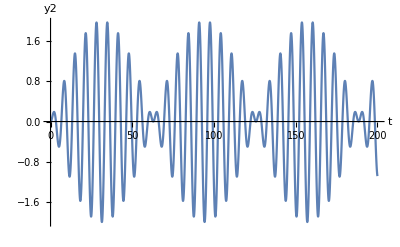

```mathematica
Plot[sol5[[1,1,2]],{t,0,200},AxesLabel->{t,y2}]
```

## RLC -Circuit::

```mathematica
(*   Li' +Ri +1/C ∫iⅆt = E0 Sin wt *)
```

```mathematica
M1 =0.1 i''[t]+100i'[t]+1000i[t]
```

1000 i[t]+100 i'[t]+0.1 i''[t]

```mathematica
q =377 155 Cos[377 t]
```

58435 Cos[377 t]

```mathematica
ihor = DSolve[M1 == 0,i[t],t]
```

{{i[t]→ⅇ^(-989.898 t) C[1]+ⅇ^(-10.1021 t) C[2]}}

```mathematica
ipartic = DSolve[{M1 == q ,i[0] == 0,i'[0]==0},i[t],t]
```

{{i[t]→(1.26293×10^-19+0.0423597 ⅈ) ⅇ^(-1000. t) ((3.7003×10^-17-12.4214 ⅈ) ⅇ^(10.1021 t)+(3.07397×10^-20+1. ⅈ) ⅇ^(989.898 t)-(3.70337×10^-17-11.4214 ⅈ) ⅇ^(1000. t) Cos[377. t]+(9.71604×10^-17-32.5885 ⅈ) ⅇ^(1000. t) Sin[377. t])}}

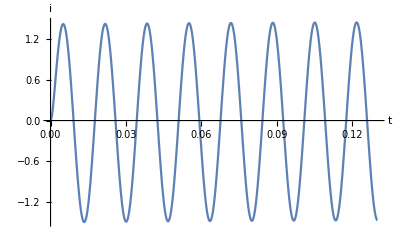

```mathematica
Plot[ipartic[[1,1,2]],{t,0,0.13},AxesLabel->{t,i}]
```

```mathematica
(* Done *)
```